```mathematica
(*E\m ratio*)
```

```mathematica
Subscript[μ, 0]=4*Pi*10^-7;
MagField[I_]:= (4/5)^(3/2)*Subscript[μ, 0]*124*I/15*10^2;
SetAttributes[MagField, Listable];
```

```mathematica
(*Data*)
r1 = {1, {40, 50, 60, 70, 80}, {2.53, 2.7, 2.85, 2.93, 3.05}};
r2 = {2, {100, 110, 120, 130, 140, 150, 160, 170, 180, 190, 200}, {2.06, 2.16, 2.23, 2.29, 2.39, 2.45, 2.51, 2.57, 2.63, 2.7, 2.76}};
r3 = {3,{100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250},{1.54, 1.58, 1.6, 1.7, 1.73, 1.78, 1.85, 1.87, 1.94, 1.98, 2.02, 2.07, 2.11, 2.15, 2.18, 2.22}};
r4 = {4, {150, 160, 170, 180, 190, 200, 210, 220, 230, 240, 250, 260, 270, 280, 290, 300}, {1.4, 1.45, 1.48, 1.52, 1.55, 1.59, 1.62, 1.65, 1.69, 1.72, 1.76, 1.79, 1.8, 1.83, 1.87, 1.89}};
```

```mathematica
(*r=1 analysis*)
r1MagField = MagField[r1[[3]]];
```

```mathematica
r1Data = Transpose[{r1[[2]],r1[[3]],r1MagField, r1em = 2*r1[[2]]/(r1[[1]]*10^-2*r1MagField)^2}];
r1Subheader = {"Acclerating Voltage (V)","Magentic current source (A)","Magnetic Field (T)", "e/m(C kg^-1)"};
r1Jointheader = StringTemplate[" r = `` cm."][r1[[1]]];
```

```mathematica
Grid[ Join[{{r1Jointheader, SpanFromLeft}}, {r1Subheader}, r1Data], Frame -> All, Alignment -> Center, Spacings -> {1,1}]
```

r = 1 cm. |  |  | 
Acclerating Voltage (V) | Magentic current source (A) | Magnetic Field (T) | e/m(C kg^-1)
40 | 2.53 | 0.0018806 | 2.26203×10^11
50 | 2.7 | 0.00200696 | 2.48269×10^11
60 | 2.85 | 0.00211846 | 2.67387×10^11
70 | 2.93 | 0.00217792 | 2.9515×10^11
80 | 3.05 | 0.00226712 | 3.11293×10^11

```mathematica
(*r=2 analysis*)
r2MagField = MagField[r2[[3]]];
```

```mathematica
r2Data = Transpose[{r2[[2]],r2[[3]],r2MagField, r2em =2*r2[[2]]/(r2[[1]]*10^-2*r2MagField)^2}];
r2Subheader = {"Acclerating Voltage (V)","Magentic current source (A)","Magnetic Field (T)", "e/m(C kg^-1)"};
r2Jointheader = StringTemplate[" r = `` cm."][r2[[1]]];
```

```mathematica
Grid[Join[{{r2Jointheader, SpanFromLeft}}, {r2Subheader}, r2Data], Frame -> All, Alignment -> Center, Spacings -> {1,1}]
```

r = 2 cm. |  |  | 
Acclerating Voltage (V) | Magentic current source (A) | Magnetic Field (T) | e/m(C kg^-1)
100 | 2.06 | 0.00153124 | 2.13248×10^11
110 | 2.16 | 0.00160557 | 2.13356×10^11
120 | 2.23 | 0.0016576 | 2.18369×10^11
130 | 2.29 | 0.0017022 | 2.24332×10^11
140 | 2.39 | 0.00177653 | 2.21795×10^11
150 | 2.45 | 0.00182113 | 2.26141×10^11
160 | 2.51 | 0.00186573 | 2.29822×10^11
170 | 2.57 | 0.00191033 | 2.32918×10^11
180 | 2.63 | 0.00195493 | 2.35494×10^11
190 | 2.7 | 0.00200696 | 2.35855×10^11
200 | 2.76 | 0.00205156 | 2.37592×10^11

```mathematica
(*r=3 analysis*)
r3MagField = MagField[r3[[3]]];
```

```mathematica
r3Data = Transpose[{r3[[2]],r3[[3]],r3MagField, r3em = 2*r3[[2]]/(r3[[1]]*10^-2*r3MagField)^2}];
r3Subheader = {"Acclerating Voltage (V)","Magentic current source (A)","Magnetic Field (T)", "e/m(C kg^-1)"};
r3Jointheader = StringTemplate[" r = `` cm."][r3[[1]]];
```

```mathematica
Grid[ Join[{{r3Jointheader, SpanFromLeft}}, {r3Subheader}, r3Data], Frame -> All, Alignment -> Center, Spacings -> {1,1}]
```

r = 3 cm. |  |  | 
Acclerating Voltage (V) | Magentic current source (A) | Magnetic Field (T) | e/m(C kg^-1)
100 | 1.54 | 0.00114471 | 1.69588×10^11
110 | 1.58 | 0.00117444 | 1.77221×10^11
120 | 1.6 | 0.00118931 | 1.88529×10^11
130 | 1.7 | 0.00126364 | 1.80918×10^11
140 | 1.73 | 0.00128594 | 1.88136×10^11
150 | 1.78 | 0.00132311 | 1.90409×10^11
160 | 1.85 | 0.00137514 | 1.88024×10^11
170 | 1.87 | 0.00139001 | 1.95525×10^11
180 | 1.94 | 0.00144204 | 1.92356×10^11
190 | 1.98 | 0.00147177 | 1.94922×10^11
200 | 2.02 | 0.0015015 | 1.97135×10^11
210 | 2.07 | 0.00153867 | 1.97113×10^11
220 | 2.11 | 0.0015684 | 1.98744×10^11
230 | 2.15 | 0.00159814 | 2.00119×10^11
240 | 2.18 | 0.00162044 | 2.03112×10^11
250 | 2.22 | 0.00165017 | 2.04019×10^11

```mathematica
(*r=4 analysis*)
r4MagField = MagField[r4[[3]]];
```

```mathematica
r4Data = Transpose[{r4[[2]],r4[[3]],r4MagField, r4em = 2*r4[[2]]/(r4[[1]]*10^-2*r4MagField)^2}];
r4Subheader = {"Acclerating Voltage (V)","Magentic current source (A)","Magnetic Field (T)", "e/m(C kg^-1)"};
r4Jointheader = StringTemplate[" r = `` cm."][r4[[1]]];
```

```mathematica
Grid[ Join[{{r4Jointheader, SpanFromLeft}}, {r4Subheader}, r4Data], Frame -> All, Alignment -> Center, Spacings -> {1,1}]
```

r = 4 cm. |  |  | 
Acclerating Voltage (V) | Magentic current source (A) | Magnetic Field (T) | e/m(C kg^-1)
150 | 1.4 | 0.00104065 | 1.73139×10^11
160 | 1.45 | 0.00107781 | 1.72164×10^11
170 | 1.48 | 0.00110011 | 1.75584×10^11
180 | 1.52 | 0.00112984 | 1.76256×10^11
190 | 1.55 | 0.00115214 | 1.78916×10^11
200 | 1.59 | 0.00118188 | 1.78976×10^11
210 | 1.62 | 0.00120418 | 1.81029×10^11
220 | 1.65 | 0.00122648 | 1.82816×10^11
230 | 1.69 | 0.00125621 | 1.82186×10^11
240 | 1.72 | 0.00127851 | 1.83533×10^11
250 | 1.76 | 0.00130824 | 1.82589×10^11
260 | 1.79 | 0.00133054 | 1.83581×10^11
270 | 1.8 | 0.00133797 | 1.88529×10^11
280 | 1.83 | 0.00136027 | 1.89154×10^11
290 | 1.87 | 0.00139001 | 1.87618×10^11
300 | 1.89 | 0.00140487 | 1.90002×10^11

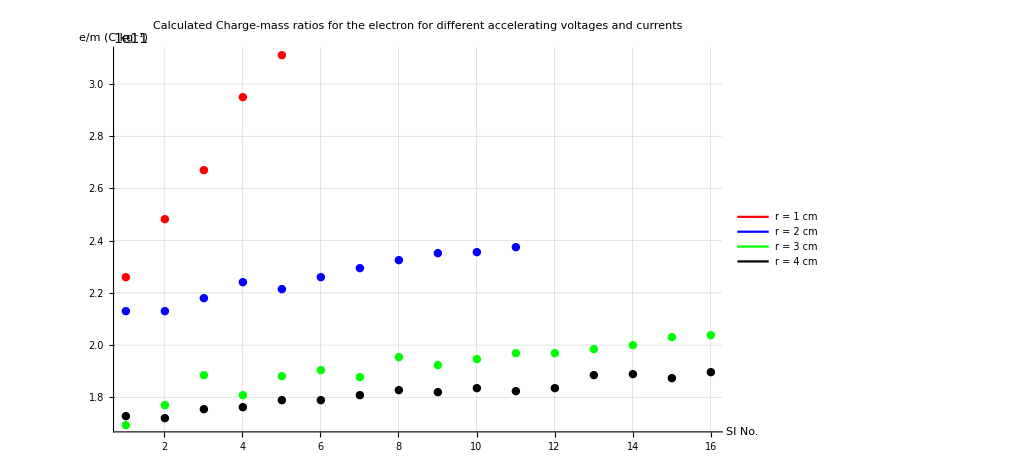

```mathematica
r1GraphData = Transpose[{Range[Length[r1em]], r1em}];
r1Plot = ListPlot[r1GraphData, PlotMarkers -> "\\[FilledCircle]", PlotStyle -> {Red, PointSize[Medium]}, GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed]];
r2GraphData = Transpose[{Range[Length[r2em]], r2em}];
r2Plot = ListPlot[r2GraphData, PlotMarkers -> "\\[FilledCircle]", PlotStyle -> {Blue, PointSize[Medium]}];
r3GraphData = Transpose[{Range[Length[r3em]], r3em}];
r3Plot = ListPlot[r3GraphData, PlotMarkers -> "\\[FilledCircle]", PlotStyle -> {Green, PointSize[Medium]}];
r4GraphData = Transpose[{Range[Length[r4em]], r4em}];
r4Plot = ListPlot[r4GraphData, PlotMarkers -> "\\[FilledCircle]", PlotStyle -> {Black, PointSize[Medium]}];
Legended[Show[r1Plot, r2Plot, r3Plot, r4Plot, PlotRange->All,AxesOrigin->{0,0}, 
PlotLabel->Style["Calculated Charge-mass ratios for the electron for different accelerating voltages and currents", Black],
AxesLabel->{"SI No.","e/m (C kg^-1)"}, AxesStyle -> Black, Background -> White, PlotStyle -> Black],
Placed[
    Framed[LineLegend[{Red, Blue, Green, Black}, {"r = 1 cm", "r = 2 cm","r = 3 cm","r = 4 cm"},  LabelStyle -> Black], Background -> White,
    FrameStyle->None],
    Right (* or use Scaled[{x, y}] for custom positioning *)
  ]
  ]
```

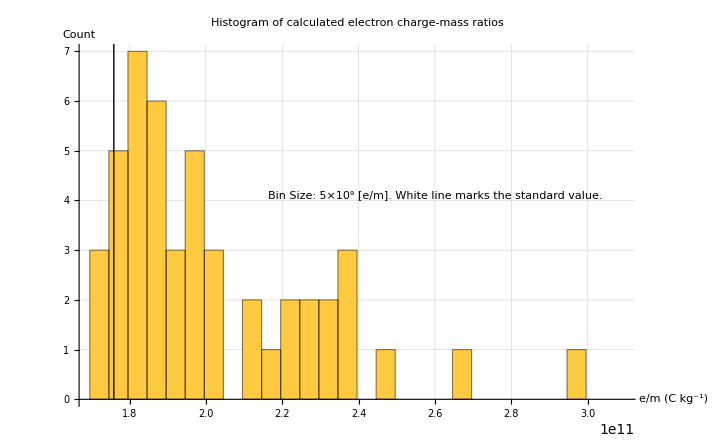

```mathematica
(*We see that our data-sets become more stable as the radius increases, even though there are 
theoretical complications involving the magnetic field expression. So we plot a histogram.*)
emHistogramData = Join[r1em,r2em,r3em,r4em];
Histogram[emHistogramData, {Min[emHistogramData],Max[emHistogramData],5*10^9}, 
AxesLabel->{"e/m (C kg^-1)","Count"}, PlotLabel->Style["Histogram of calculated electron charge-mass ratios", Black],
Epilog -> {Text[Style["Bin Size: 5×10^9 [e/m]. White line marks the standard value.", Black],{2.6*10^11,4.1}], Black, Thick, Line[{{1.75882*10^11, 0}, {1.75882*10^11, 13}}]}, GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed]
,Background -> White, AxesStyle -> Black]
(*White line marks the standard value*)
```

```mathematica
(*Decidedly not gaussian, though peaking somewhere between 1.8×10^11 and 1.9×10^11. 
Treating these as independent measurements, and ignoring the r = 1cm case (due to its relatively extreme variance), the combined mean value and standard deviation for the e/m ratio is given as follows *)
```

```mathematica
r1Mean=Mean[r1em]; r1Stddev=Sqrt[r1Var = Variance[r1em]];
r2Mean=Mean[r2em]; r2Stddev=Sqrt[r2Var = Variance[r2em]];
r3Mean=Mean[r3em]; r3Stddev=Sqrt[r3Var = Variance[r3em]];
r4Mean=Mean[r4em]; r4Stddev=Sqrt[r4Var = Variance[r4em]];

IndividualComparisonData = {{r1Mean, r1Stddev},{r2Mean, r2Stddev},{r3Mean, r3Stddev},{r4Mean,r4Stddev}};
TableForm[IndividualComparisonData, TableHeadings->{{"r = 1 cm","r = 2 cm","r = 3 cm","r = 4 cm"},{"Mean","Std. deviation"}}]
```

| Mean | Std. deviation
r = 1 cm | 2.6966×10^11 | 3.44032×10^10
r = 2 cm | 2.26266×10^11 | 8.85733×10^9
r = 3 cm | 1.91617×10^11 | 9.44957×10^9
r = 4 cm | 1.81629×10^11 | 5.55036×10^9

```mathematica
emCombinedMean = (r2Mean/r2Var+r3Mean/r3Var+r4Mean/r4Var)/(1/r2Var+1/r3Var+1/r4Var);
emCombinedVariance = Sqrt[1/(1/r2Var+1/r3Var+1/r4Var)];
Print["The combined mean for the calculated e/m and its standard deviation are ", emCombinedMean, "C kg^-1 and ", emCombinedVariance, " C kg^-1, respectively."]
```

The combined mean for the calculated e/m and its standard deviation are 1.93699×10^11C kg^-1 and 4.21053×10^9 C kg^-1, respectively.

```mathematica
(* For the r=4 data set alone, though...*)
Print["The r=4 mean for the calculated e/m and its standard deviation are ", r4Mean, "C kg^-1 and ", Sqrt[r4Var], " C kg^-1, respectively."]
(*Much closer to the standard value*)
```

The r=4 mean for the calculated e/m and its standard deviation are 1.81629×10^11C kg^-1 and 5.55036×10^9 C kg^-1, respectively.